Plot of the example curves shown in Fig. 4c.

```mathematica
θ1=Flatten[Import[NotebookDirectory[]<>"ExampleCurves/curve_1.csv"]][[2;;]];
θ2=Flatten[Import[NotebookDirectory[]<>"ExampleCurves/curve_2.csv"]][[2;;]];
θ3=Flatten[Import[NotebookDirectory[]<>"ExampleCurves/curve_3.csv"]][[2;;]];
```

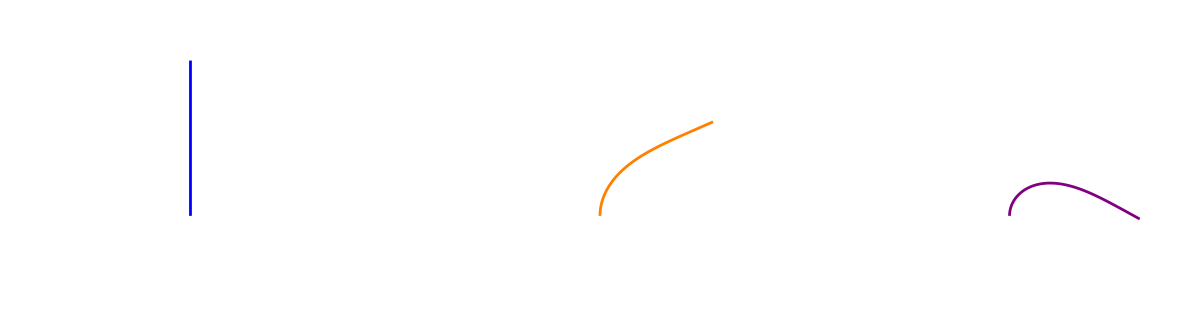

```mathematica
F1=Interpolation[Table[{(s-1)/Length[θ1],θ1[[s]]},{s,1,Length[θ1]}]];
F2=Interpolation[Table[{(s-1)/Length[θ2],θ2[[s]]},{s,1,Length[θ2]}]];
F3=Interpolation[Table[{(s-1)/Length[θ3],θ3[[s]]},{s,1,Length[θ3]}]];Num1=NDSolve[{X'[θ]==Cos[F1[θ]+π/2],Y'[θ]==Sin[F1[θ]+π/2],X[0]==0,Y[0]==0},{X,Y},{θ,0,(Length[θ1]-1)/Length[θ1]}];
Num2=NDSolve[{X'[θ]==Cos[F2[θ]+π/2],Y'[θ]==Sin[F2[θ]+π/2],X[0]==0,Y[0]==0},{X,Y},{θ,0,(Length[θ2]-1)/Length[θ2]}];Num3=NDSolve[{X'[θ]==Cos[F3[θ]+π/2],Y'[θ]==Sin[F3[θ]+π/2],X[0]==0,Y[0]==0},{X,Y},{θ,0,(Length[θ3]-1)/Length[θ3]}];p1=GraphicsRow[{ParametricPlot[{Evaluate[{X[ϕ],Y[ϕ]}/.Num1]},{ϕ,0,1},PlotRange->{{-1,1},{-0.5,1.2}},Frame->False,Axes->False,PlotStyle->Blue],
ParametricPlot[{Evaluate[{X[ϕ],Y[ϕ]}/.Num2]},{ϕ,0,1},PlotRange->{{-1,1},{-0.5,1.2}},Frame->False,Axes->False,PlotStyle->Orange],
ParametricPlot[{Evaluate[{X[ϕ],Y[ϕ]}/.Num3]},{ϕ,0,1},PlotRange->{{-1,1},{-0.5,1.2}},Frame->False,Axes->False,PlotStyle->Purple]}]
```

```mathematica
Export[NotebookDirectory[]<>"ExampleCurves/Example_Curves.svg",p1,ImageResolution->600]
```